# 实验习题2

## 工科数学分析——数学实验

## 题1

#### 用图形法求方程的根

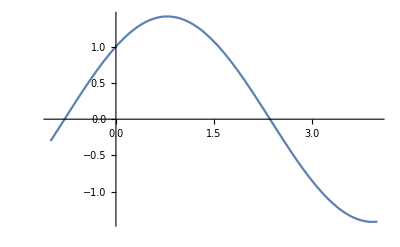

```mathematica
f[x_]:=Cos[x]+Sin[x];
Plot[f[x],{x,-1,4}]
```

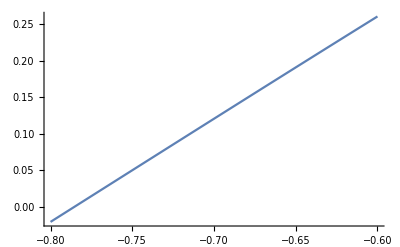

```mathematica
Plot[f[x],{x,-0.8,-0.6},PlotRange->Full]
```

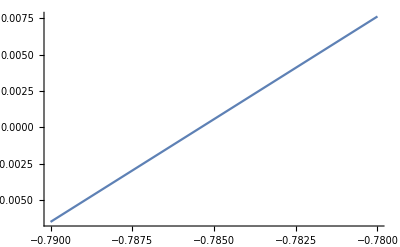

```mathematica
Plot[f[x],{x,-0.79,-0.78},PlotRange->Full]
```

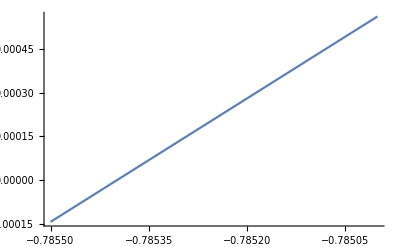

```mathematica
Plot[f[x],{x,-0.7855,-0.7850},PlotRange->Full]
```

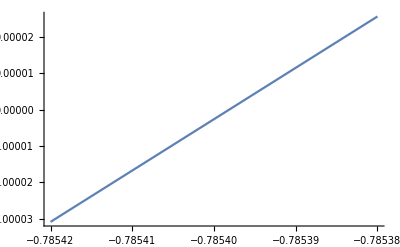

```mathematica
Plot[f[x],{x,-0.78542,-0.78538},PlotRange->Full]
```

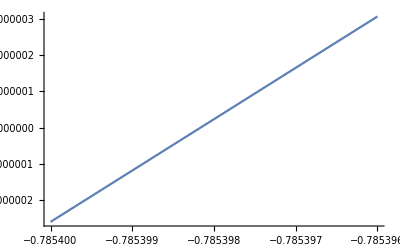

```mathematica
Plot[f[x],{x,-0.785400,-0.785396},PlotRange->Full]
```

```mathematica
选取 （-0.7853982，-0.7853980） 的端点作为方程的第一个根，误差不会超过10^（-6 ）。
```

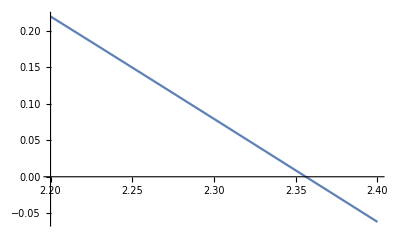

```mathematica
Plot[f[x],{x,2.2,2.4},PlotRange->Full]
```

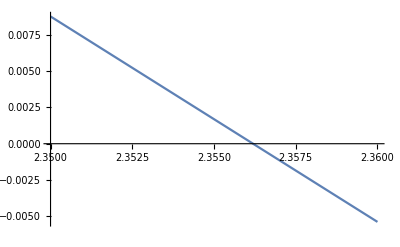

```mathematica
Plot[f[x],{x,2.35,2.36},PlotRange->Full]
```

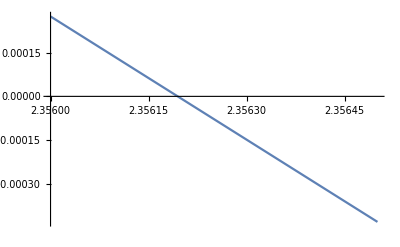

```mathematica
Plot[f[x],{x,2.3560,2.3565},PlotRange->Full]
```

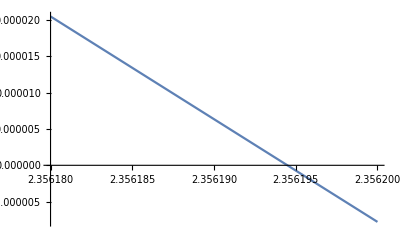

```mathematica
Plot[f[x],{x,2.35618,2.35620},PlotRange->Full]
```

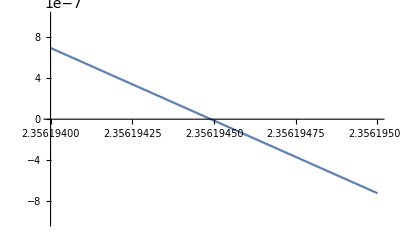

```mathematica
Plot[f[x],{x,2.356194,2.356195},PlotRange->{-10^(-6),10^(-6)}]
```

```mathematica
选取 （2.356192，2.356192） 的端点作为方程的第二个根，误差不会超过10^（-6）。
```

### 用二分法求方程的根

```mathematica
a0=-1;b0=0;c0=2;d0=3;delta=10^(-6);k0=25;
a=a0;b=b0;
Do[x=(a+b)/2;Print["x=",N[x,17],"    n=",k];
If[f[x]==0,Break[],If[f[x]*f[a]<0,b=x,a=x]];
If[Abs[b-a]<delta,Break[],If[k==k0,Print["迭代次数达不到要求精度。"]]],
{k,k0}
]
```

x=-0.5    n=1

x=-0.75    n=2

x=-0.875    n=3

x=-0.8125    n=4

x=-0.78125    n=5

x=-0.796875    n=6

x=-0.7890625    n=7

x=-0.78515625    n=8

x=-0.787109375    n=9

x=-0.7861328125    n=10

x=-0.78564453125    n=11

x=-0.785400390625    n=12

x=-0.7852783203125    n=13

x=-0.78533935546875    n=14

x=-0.785369873046875    n=15

x=-0.7853851318359375    n=16

x=-0.78539276123046875    n=17

x=-0.78539657592773438    n=18

x=-0.78539848327636719    n=19

x=-0.78539752960205078    n=20
选取-0.78539752960205078作为方程的第一个根，误差不会超过10^（-6）。

```mathematica
c=c0;d=d0;
Do[x=(c+d)/2;Print["x=",N[x,17],"    n=",k];
If[f[x]==0,Break[],If[f[x]*f[c]<0,d=x,c=x]];
If[Abs[d-c]<delta,Break[],If[k==k0,Print["迭代次数达不到要求精度。"]]],
{k,k0}
]
```

x=2.5    n=1

x=2.25    n=2

x=2.375    n=3

x=2.3125    n=4

x=2.34375    n=5

x=2.359375    n=6

x=2.3515625    n=7

x=2.35546875    n=8

x=2.357421875    n=9

x=2.3564453125    n=10

x=2.35595703125    n=11

x=2.356201171875    n=12

x=2.3560791015625    n=13

x=2.35614013671875    n=14

x=2.356170654296875    n=15

x=2.3561859130859375    n=16

x=2.3561935424804688    n=17

x=2.3561973571777344    n=18

x=2.3561954498291016    n=19

x=2.3561944961547852    n=20
选取2.3561944961547852作为方程的第二个根，误差不会超过10^（-6）。

## 题2

### 用切线迭代法求方程的根

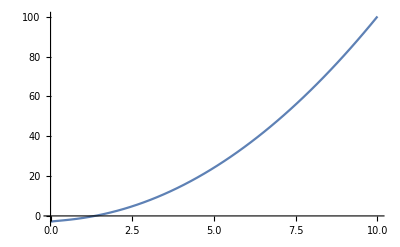

```mathematica
g[x_]:=x^2+√x-3;
Plot[g[x],{x,0,10}]
```

```mathematica
可见在区间 （1，2） 上可以使用切线迭代法求方程的根。
```

```mathematica
a=1;b=2;delta=10^(-6);k0=20;
m=Min[g'[a],g'[b]];
If[g[a]*g'[a]>0,x0=a,x0=b];
Do[x=x0-(g(x0))/(g'(x0));Print["x=",N[x,17],"   n=",k];
If[Abs[g(x)]<delta *m,Break[],
If[k<k0,x0=x,Print["迭代次数不能满足精度要求。"]]],{k,k0}
]
```

x=1.4454613632189539   n=1

x=1.3572698081601986   n=2

x=1.3549793466560025   n=3

x=1.3549778078301181   n=4

```mathematica
选取1 .3549778078301181 作为方程的解，误差不会超过10^(-6)。
```